Quiz 1

```mathematica
(*1*)k=N[Pi^2/6,100]
```

1.644934066848226436472415166646025189218949901206798437735558229370007470403200873833628900619758705

```mathematica
ResourceFunction["NthDigit"][k,100]
```

5

```mathematica
(*2*)Solve[x^5-Exp[x/4]==0,x,Reals]//N
```

{{x→1.05412},{x→89.9951}}

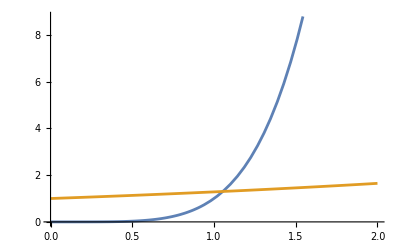

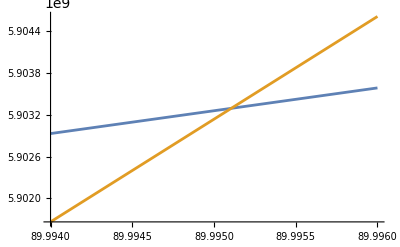

```mathematica
Plot[{x^5,Exp[x/4]},{x,0,2}]
Plot[{x^5,Exp[x/4]},{x,89.994,89.996}]
```

```mathematica
(*3*)f[x_]=1/x^6-10/x^5
```

1/x^6-10/x^5

```mathematica
critic=Solve[D[f[x],x]==0,x]//N
```

{{x→0.12}}

```mathematica
doubleder=D[f[x],{x,2}]/.critic(*Positive => Minima*)
```

{1.39541×10^8}

```mathematica
Taylor[x_]=(f[x]/.critic)+doubleder*(x-0.12)^2
```

{-66979.6+1.39541×10^8 (-0.12+x)^2}

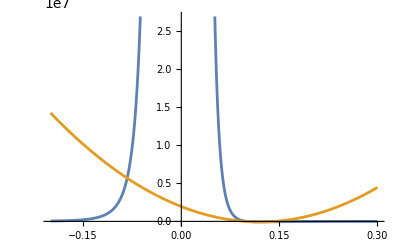

```mathematica
Plot[{f[x],Taylor[x]},{x,-0.2,0.3}]
```

```mathematica
(*4*)Manipulate[Plot[1/(x^2-a^2),{x,-5,5}],{a,1,4}]
(*Divergence x = a,-a
Zeroes DNE
Extrema Local maximum of -1/a^2 at x = 0
Assymptotes Vetrical x = a,-a; Horizontal y = 0 *)
```

```mathematica
Manipulate[D[1/(x^2-a^2), x],{a,0,5}]
```

```mathematica
(*5*)Manipulate[Solve[r-x-x^3+x^4/2==0,x,Reals],{r,-5,5}](*[r<2.4]Lower x is stable fixed pt, higher x is unstable fixed pt
[r>=2.4]No fixed point*)
```

```mathematica
Manipulate[Plot[r-x-x^3+x^4/2,{x,-5,5},PlotRange->{{-5,5},{-10,10}}],{r,-5,5}]
```

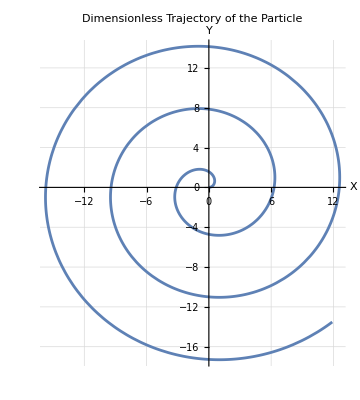

```mathematica
(*6*)T=t;

(*Define dimensionless x and y*)
X[t_]:=(t^2/2) Cos[t^2/2];
Y[t_]:=(t^2/2) Sin[t^2/2];

(*Plot the trajectory*)
ParametricPlot[{X[t],Y[t]},{t,0,6},PlotRange->All,AxesLabel->{"X","Y"},PlotLabel->"Dimensionless Trajectory of the Particle",GridLines->Automatic]
```

```mathematica
(*7 - Assume 1/(4 Subscript[πϵ, 0]) = 1*)
Manipulate[VectorPlot[{q1/(x+10)^2+q2/x^2+q3/(x-10)^2,(q1+q2+q3)/x^2},{x,-20,20},{y,-20,20}],{{q1,0},-5,5},{{q2,0},-5,5},{{q3,0},-5,5}]
```

```mathematica
PolarPlot[Sin[2 θ]+Cos[2θ],{θ,0,2 Pi},PlotLabels->"Expressions"]
```

-Graphics-

```mathematica
Mid-Sem
```

```mathematica
V[r_]=-1/r^2+2/r^4;
Mini=Solve[D[V[r],r]==0,r]
```

{{r→-2},{r→2}}

```mathematica
D[V[r],{r,2}]/.Mini(*Both are minima*)
```

{1/4,1/4}

```mathematica
α=V[r]/.Mini[[2]]
```

-1/8

```mathematica
x[0]=2.0; (*initial value*)
For[i=0,i<1000,i++,x[i+1]=0.5 x[i]+2 Log[x[i]]]

x[1000]
```

8.61317

```mathematica
(*Define the dimensionless potential*)
U[rho_]:=2/rho-1/rho^2;

(*Compute the Taylor expansion around rho = 1 up to quadratic order*)
taylorSeries=Series[U[rho],{rho,1,2}]

(*Convert series to polynomial*)
Uapprox[rho_]=Normal[taylorSeries]
```

1-(rho-1)^2+O[rho-1]^3

1-(-1+rho)^2

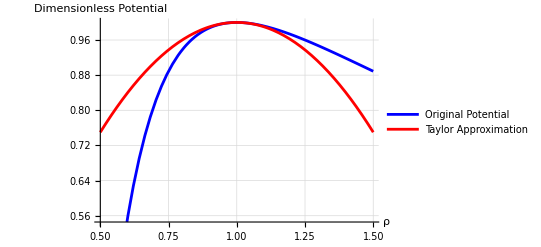

```mathematica
(*Plot both the original potential and the Taylor approximation*)
Plot[{U[rho],Evaluate[Uapprox[rho]]},{rho,0.5,1.5},PlotLegends->{"Original Potential","Taylor Approximation"},PlotStyle->{Blue,Red},AxesLabel->{"ρ","Dimensionless Potential"},GridLines->Automatic]
```

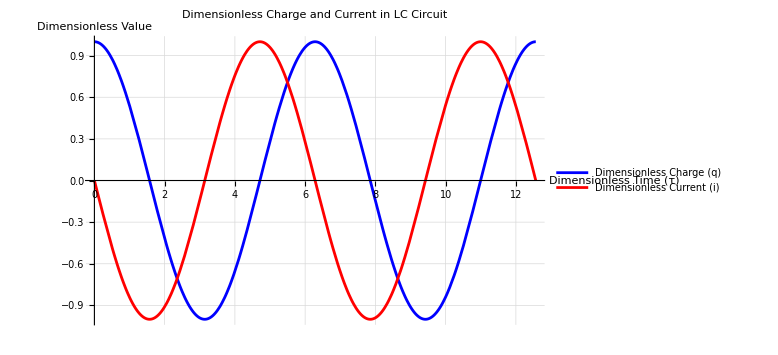

```mathematica
(*Define dimensionless charge and current*)
q[tau_]:=Cos[tau]
i[tau_]:=-Sin[tau]

(*Plot dimensionless charge and current vs dimensionless time*)
(*Plotting over two periods (0 to 4*Pi)*)
Plot[{q[tau],i[tau]},(*Functions to plot*){tau,0,4*Pi},(*Plot range for dimensionless time*)PlotLegends->{"Dimensionless Charge (q)","Dimensionless Current (i)"},(*Legend*)PlotStyle->{Blue,Red},(*Colors for the curves*)AxesLabel->{"Dimensionless Time (τ)","Dimensionless Value"},(*Axes labels*)PlotLabel->"Dimensionless Charge and Current in LC Circuit",(*Plot title*)GridLines->Automatic,(*Add grid lines*)ImageSize->Large (*Make the plot larger*)]
```

```mathematica
DSolve[{x''[t]+x'[t]+x[t]==0,(*Differential Equation*)
x[0]==1,(*Initial Condition for x*)
x'[0]==0},(*Initial Condition for x'*)
x[t],(*Function to solve for*)
t                             (*Independent variable*)]
```

{{x[t]→1/3 ⅇ^(-t/2) (3 Cos[(√3 t)/2]+√3 Sin[(√3 t)/2])}}

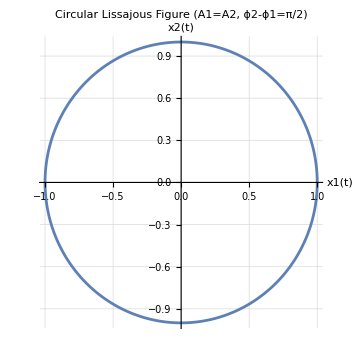

```mathematica
(*Parameters for a circular Lissajous figure*)A1=1;
A2=1; (*Condition:A1=A2*)
omega=1; (*Angular frequency*)
phi1=0; (*Phase for x1*)
phi2=Pi/2; (*Phase for x2,Condition:phi2-phi1=+/-Pi/2*)

(*Define the parametric equations*)
x1[t_]:=A1 Cos[omega t+phi1]
x2[t_]:=A2 Cos[omega t+phi2]

(*Plot the Lissajous figure*)
ParametricPlot[{x1[t],x2[t]},(*Parametric functions {x,y}*){t,0,2 Pi/omega},(*Parameter range (one full cycle)*)PlotLabel->"Circular Lissajous Figure (A1=A2, ϕ2-ϕ1=π/2)",AxesLabel->{"x1(t)","x2(t)"},AspectRatio->Automatic,(*Crucial for showing a true circle*)GridLines->Automatic]
```